```mathematica
Clear[flipbook]
flipbook={};
For[n=0,n≤700,n++,
data=Import["//Users/diegolallemand/phys/med/project/output/all/grain"<>ToString[n]<>".txt","Table"];
list={};
For[i=1,i≤Length[data],i++,
x=data[[i]][[2]];
y=data[[i]][[3]];
a=data[[i]][[6]];
r=data[[i]][[7]];

list=Join[list,{{Gray,Disk[{x,y},r]},{Black,Arrowheads[0.01],Arrow[{{x,y},{x,y}+r*{Cos[a],Sin[a]}}]}}];
];
flipbook = Join[flipbook,{Graphics[list]}];
]; 
anim=ListAnimate[flipbook]
Export["/Users/diegolallemand/phys/med/presentation/figure/oscillation.mp4",anim,"AnimationDuration"-> 7,AnimationRate->10]
```

```mathematica
Export["/Users/diegolallemand/phys/med/presentation/figure/oscillation.mp4",anim,"AnimationDuration"-> 7,AnimationRate->10]
```

/Users/diegolallemand/phys/med/presentation/figure/oscillation.mp4

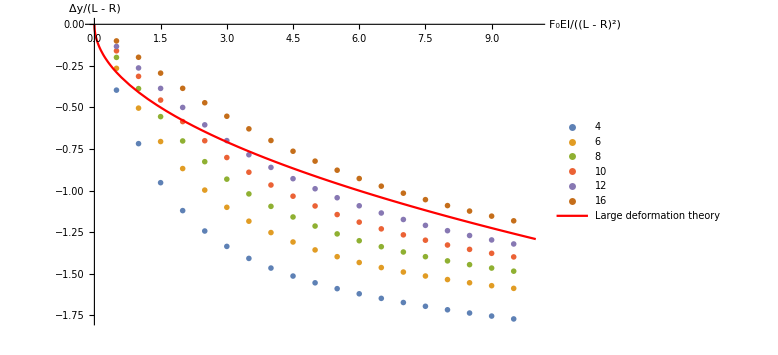

/Users/diegolallemand/phys/med/presentation/figure/evol_y0_F0.pdf

```mathematica
data1 = Import["/Users/diegolallemand/phys/med/project/output/ft_v_4.txt","Table"];
data2 = Import["/Users/diegolallemand/phys/med/project/output/ft_v_6.txt","Table"];
data3 = Import["/Users/diegolallemand/phys/med/project/output/ft_v_8.txt","Table"];
data4 = Import["/Users/diegolallemand/phys/med/project/output/ft_v_10.txt","Table"];
data5 = Import["/Users/diegolallemand/phys/med/project/output/ft_v_12.txt","Table"];
data6 = Import["/Users/diegolallemand/phys/med/project/output/ft_v_16.txt","Table"];

a=ListPlot[{data1,data2,data3,data4,data5,data6},
PlotLegends->{"4","6","8","10","12","16"},
PlotMarkers->"OpenMarkers",
AxesLabel->{"F_0EI/(L - R)^2","Δy/(L - R)"},
LabelStyle->{FontSize->14},
ImageSize->Large];

L=1;
Young=10^6;
mass=0.01875;
radius=0.0625;
Inertia=π*radius^4 /4;
deflect[x_]:=-Sqrt[2]*Sqrt[x/(Young Inertia L)]
b=Plot[deflect[x],{x,0,10},PlotLegends->{"Large deformation theory"},PlotStyle->{Red}];

graph=Show[a,b,PlotRange->{{0,10},All},PlotLegends->Placed[{"4","6","8","10","12","16","Déflexion Théorique"},Below]]

Export["/Users/diegolallemand/phys/med/presentation/figure/evol_y0_F0.pdf",graph]
```

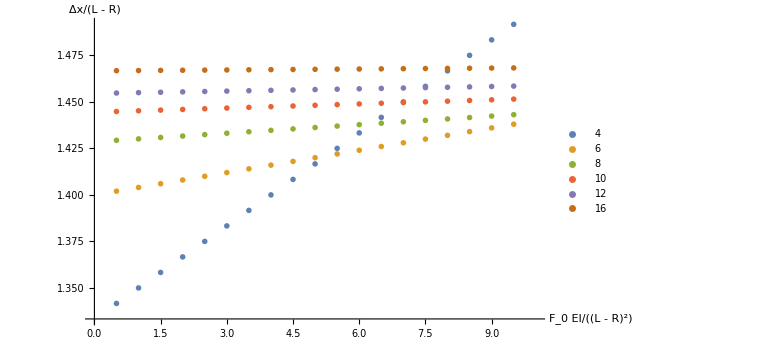

/Users/diegolallemand/phys/med/presentation/figure/evol_x0_F0.pdf

```mathematica
data1 = Import["/Users/diegolallemand/phys/med/project/output/ft_h_4.txt","Table"];
data2 = Import["/Users/diegolallemand/phys/med/project/output/ft_h_6.txt","Table"];
data3 = Import["/Users/diegolallemand/phys/med/project/output/ft_h_8.txt","Table"];
data4 = Import["/Users/diegolallemand/phys/med/project/output/ft_h_10.txt","Table"];
data5 = Import["/Users/diegolallemand/phys/med/project/output/ft_h_12.txt","Table"];
data6 = Import["/Users/diegolallemand/phys/med/project/output/ft_h_16.txt","Table"];

graph=ListPlot[{data1,data2,data3,data4,data5,data6},PlotRange->{{0,10},All},
PlotLegends->{"4","6","8","10","12","16"},
PlotMarkers->"OpenMarkers",
AxesLabel->{"F_0 EI/(L - R)^2","Δx/(L - R)"},
LabelStyle->{FontSize->10},
ImageSize->Large]
Export["/Users/diegolallemand/phys/med/presentation/figure/evol_x0_F0.pdf",graph]
```

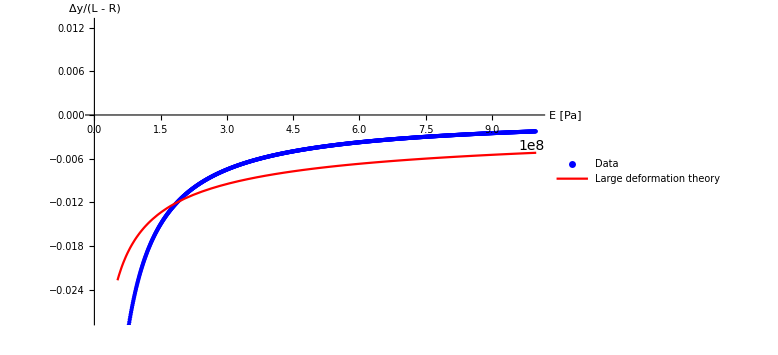

/Users/diegolallemand/phys/med/presentation/figure/evol_E.pdf

```mathematica
data=Import["/Users/diegolallemand/phys/med/project/output/evol_E.txt","Table"];
d=ListPlot[data,PlotStyle->{Blue,PointSize[Medium]},PlotLegends->{"Data"}];

L=1;
Young=10^6;
mass=0.8333;
radius=0.08333;
Inertia=Pi*radius^4*4;

deflect[x_]:=-√2 Sqrt[9.81*mass/(x*Inertia*L)];

p=Plot[deflect[x],{x,10^3,10^9},PlotStyle->{Red,Thick},PlotLegends->{"Large deformation theory"}];

graph=Show[d,p,AxesLabel->{"E [Pa]","Δy/(L - R)"},
PlotLegends->Placed[{"Data","Large deformation theory"},{0.75,0.85}],
ImageSize->Large];
graph
Export["/Users/diegolallemand/phys/med/presentation/figure/evol_E.pdf",graph]
```

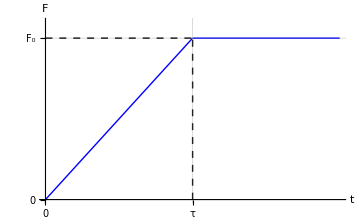

/Users/diegolallemand/phys/med/presentation/figure/loading_history.pdf

```mathematica
loadingHistory[t_,tMax_,Fn_]:=Piecewise[{{Fn*(t/tMax),0<=t<=tMax},{Fn,t>tMax}}]

tMax=1;
Fn=1;

plot=Plot[loadingHistory[t,tMax,Fn],{t,0,2*tMax},PlotRange->{0,Fn+0.1},AxesLabel->{"t",Style["F",Italic]},Ticks->{{{0,"0"},{tMax,"τ"}},{{0,"0"},{Fn,"F_0"}}},PlotStyle->{Blue,Thick},AxesOrigin->{0,0},GridLines->Automatic,Epilog->{Dashed,Line[{{tMax,0},{tMax,Fn}}],Line[{{0,Fn},{tMax,Fn}}]},ImageSize->Medium]

Export["/Users/diegolallemand/phys/med/presentation/figure/loading_history.pdf",plot]
```

```mathematica
data1=Import["/Users/diegolallemand/phys/med/project/output/evol_phi_clock.txt","Table"];
data2=Import["/Users/diegolallemand/phys/med/project/output/evol_phi_anticlock.txt","Table"];
graph=ListPlot[{data1,data2},
AxesLabel->{"ϕ","θ-θ_0"},
PlotLegends->Placed[{"Data"},{1,0.85}],
LabelStyle->{FontSize->12},
Ticks->{{0,20,40,60,80,100,120,140,160,180},{}},
ImageSize->Large];
graph
Export["/Users/diegolallemand/phys/med/presentation/figure/evol_phi_test.pdf",graph]
```

-Graphics-

/Users/diegolallemand/phys/med/presentation/figure/evol_phi_test.pdf

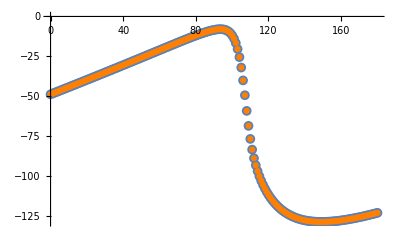

/Users/diegolallemand/phys/med/presentation/figure/no_hysteresis.pdf

```mathematica
data1=Import["/Users/diegolallemand/phys/med/project/output/test.txt","Table"];
data2=Import["/Users/diegolallemand/phys/med/project/output/test2.txt","Table"];
a=ListPlot[data1,PlotMarkers->{Automatic,Medium},PlotLegends->"anti-clockwise"];
b=ListPlot[data2,PlotMarkers->{Automatic,Smaller},PlotLegends->"clockwise",PlotStyle->{Orange}];
graph =Show[a,b,PlotLegends->Placed[{"anti-clockwise","clockwise"},LegendMarkers->{"Bubble"},Below]]
Export["/Users/diegolallemand/phys/med/presentation/figure/no_hysteresis.pdf",graph]
```

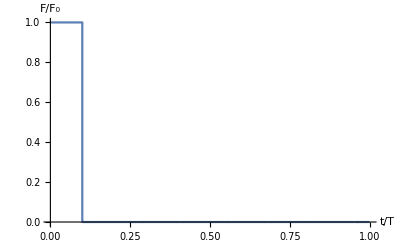

/Users/diegolallemand/phys/med/presentation/figure/loading_force.pdf

```mathematica
data1=Import["/Users/diegolallemand/phys/med/project/output/test.txt","Table"];
graph=ListLinePlot[data1,
AxesLabel->{,}]
Export["/Users/diegolallemand/phys/med/presentation/figure/loading_force.pdf",graph]
```

```mathematica
data1=Import["/Users/diegolallemand/phys/med/project/output/test1.txt","Table"];
data2=Import["/Users/diegolallemand/phys/med/project/output/test2.txt","Table"];
data3=Import["/Users/diegolallemand/phys/med/project/output/test3.txt","Table"];
data4=Import["/Users/diegolallemand/phys/med/project/output/test4.txt","Table"];
graph =ListLinePlot[{data1,data2,data3,data4},
ImageSize->Large,
AxesLabel->{"",""},
LabelStyle->{FontSize->14},
PlotStyle->{FontSize->10},
PlotLegends->{"3","6","9","12"},
Ticks->{{1,2,3,4,5,6,7,8},{-1,-0.5,0.5,1}},
PlotRange->{{0,5},All}];
graph
Export["/Users/diegolallemand/phys/med/presentation/figure/oscillation.pdf",graph]
```

-Graphics-

/Users/diegolallemand/phys/med/presentation/figure/oscillation.pdf

```mathematica
L=1;
Young=10^7;
mass=0.8333;
radius=0.08333;
Inertia=Pi*radius^4/2;
1.7868* √((12*0.8333)/(Young I))
```

0.00126343-0.00126343 ⅈ

```mathematica
Clear[flipbook]
flipbook={};
For[n=0,n<=700,n++,data=Import["/Users/diegolallemand/phys/med/project/output/all/grain"<>ToString[n]<>".txt","Table"];
list={};
For[i=1,i<=Length[data],i++,x=data[[i]][[2]];
y=data[[i]][[3]];
a=data[[i]][[6]];
r=data[[i]][[7]];
list=Join[list,{{Gray,Disk[{x,y},r]},{Black,Arrowheads[0.01],Arrow[{{x,y},{x,y}+r*{Cos[a],Sin[a]}}]}}];];
flipbook=Join[flipbook,{Graphics[list]}];];
anim=ListAnimate[flipbook,AnimationRepetitions->1]

Export["/Users/diegolallemand/phys/med/presentation/figure/oscillation.mp4",flipbook,"AnimationDuration"->35,"FrameRate"->10]
```

/Users/diegolallemand/phys/med/presentation/figure/oscillation.mp4